```mathematica
stopsign1=ImageResize[-Graphics-,1200*30/160];
```

```mathematica
stopsign1
```

-Graphics-

```mathematica
stop=Table[(ImageValue[stopsign1,{x+112,y+112}]//Norm)/Sqrt[3],{y,-105,+105},{x,-105,+105}]//DispImage;
```

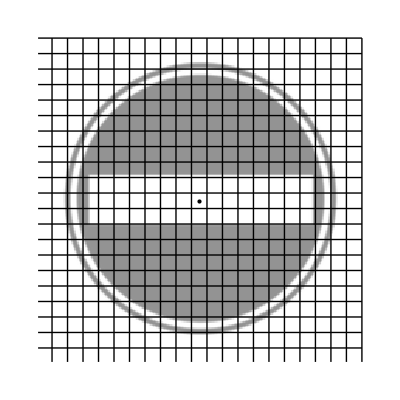

```mathematica
Show[{stop,
Table[Graphics[Line[{{1,y*10},{210,y*10}}]],{y,1,21}],
Table[Graphics[Line[{{x*10,1},{x*10,210}}]],{x,1,21}],
Point[{105,105}]//Graphics}]
```

```mathematica
ImageDimensions[stopsign1]
```

{225,225}

```mathematica
(({213,681}+{981,681}+{206,520}+{981,515})/4.)*30/160
```

{111.609,112.359}

```mathematica
ImageDimensions[stopsign1]
```

{1200,1200}

```mathematica
30/160//N
```

0.1875